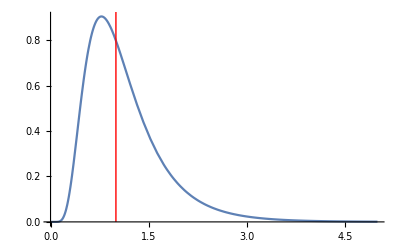

```mathematica
lineStyle = {Thick, Red};
line1 = Line[{{1, 0}, {1, 2}}];
Plot[PDF[LogNormalDistribution[0, 0.5], x], {x, 0, 5}, Epilog -> {Directive[lineStyle], line1}]
```

```mathematica
Solve[Expectation[x, x \[Distributed] LogNormalDistribution[u, 0.5]]==1, {u}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{u→-0.125}}

```mathematica
Expectation[x, x \[Distributed] LogNormalDistribution[-0.125, 0.5]]//N
```

1.

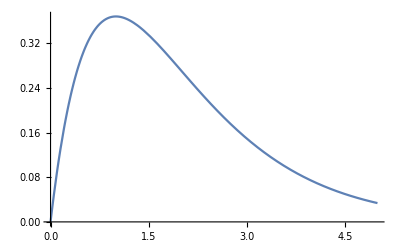

```mathematica
Plot[PDF[GammaDistribution[2, 1], x], {x, 0, 5}]
```

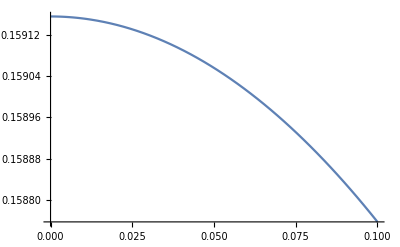

```mathematica
lineStyle = {Thick, Red};
line1 = Line[{{1, 0}, {1, 2}}];
Plot[PDF[CauchyDistribution[0, 2], x], {x, 0, 3}, Epilog -> {Directive[lineStyle], line1}]
```

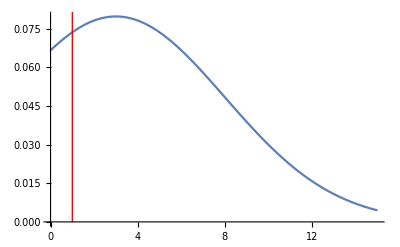

```mathematica
lineStyle = {Thick, Red};
line1 = Line[{{1, 0}, {1, 2}}];
Plot[PDF[NormalDistribution[3, 5], x], {x, 0, 15}, Epilog -> {Directive[lineStyle], line1}]
```

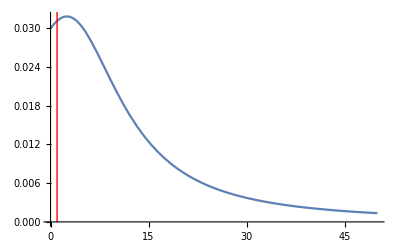

```mathematica
lineStyle = {Thick, Red};
line1 = Line[{{1, 0}, {1, 2}}];
Plot[PDF[CauchyDistribution[2.5, 10], x], {x, 0, 50}, Epilog -> {Directive[lineStyle], line1}]
```

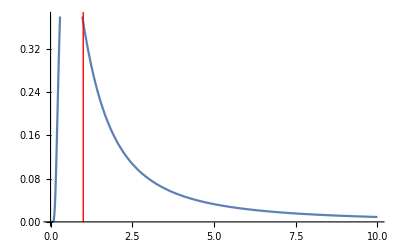

```mathematica
lineStyle = {Thick, Red};
line1 = Line[{{1, 0}, {1, 2}}];
Plot[PDF[InverseGammaDistribution[1, 1], x], {x, 0, 10}, Epilog -> {Directive[lineStyle], line1}]
```